```mathematica
s = NDSolve[{
x''[t]-1000(1-x'[t]^2)x'[t]+x[t]==0,
x[0]==0,
x'[0]==0.001
}, x[t], {t,0,1000}]
```

{{x[t]→InterpolatingFunction[…][t]}}

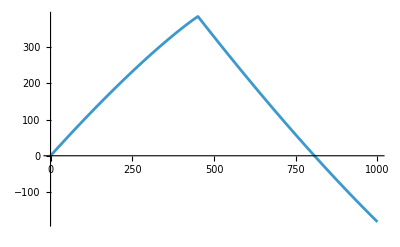

```mathematica
Plot[Evaluate[x[t]/.s],{t,0,1000},PlotRange->All]
```

```mathematica
Evaluate[x[t]/.s]/.t->1000
```

{-182.783}

```mathematica
s = NDSolve[{
y''[x]+(x^2-3)y'[x]+(x^2-3)Cos[x]y[x]== 2- 6x+2 x^3 +(x^2-3)E^x Sin[x](1+Cos[x])+Cos[x](E^x+(x^2-1)+x^4-3 x^2),
y[0]==0,
y[Pi]==Pi^2
}, y[x], {x,0,Pi}]
```

{{y[x]→InterpolatingFunction[…][x]}}

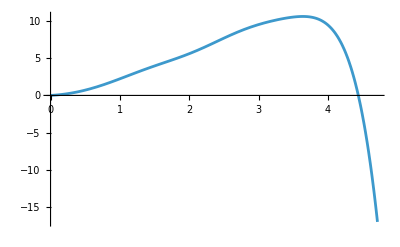

```mathematica
Plot[Evaluate[y[x]/.s],{x,0,Pi},PlotRange->All]
```

```mathematica
Table[Evaluate[y[x]/.s],{x,{0.5,1,1.5,2,2.5}}]
```

{{0.710184},{2.22906},{3.95431},{5.59819},{7.68426}}